## Example 4.1

### Chebyshev

```mathematica
Tit[Tn_,Tnm1_, x_]=2 x Tn - Tnm1
TitM[Tn_,Tnm1_, x_]=2 x.Tn - Tnm1
```

-Tnm1+2 Tn x

-Tnm1+2 x.Tn

```mathematica
T1 = x
T2=Tit[x,1, x]
```

x

-1+2 x^2

```mathematica
T3=Tit[T2,T1, x]//FullSimplify
```

x (-3+4 x^2)

```mathematica
T4=Tit[T3,T2, x]//FullSimplify
```

1-8 x^2+8 x^4

```mathematica
T1M[x_]:=x
T2M[x_]:=FullSimplify[2 x.x - IdentityMatrix[Length[x]]]
T3M[x_]:=FullSimplify[TitM[T2M[x],T1M[x], x]]
T4M[x_]:=FullSimplify[TitM[T3M[x],T2M[x], x]]
T5M[x_]:=FullSimplify[TitM[T4M[x],T3M[x], x]]
```

### Comparison

```mathematica
H = 1/Sqrt[2]{{1,1},{1,-1}}
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
Uexact[t_]=MatrixExp[-I t H]//FullSimplify
```

{{Cos[t]-(ⅈ Sin[t])/(√2),-(ⅈ Sin[t])/(√2)},{-(ⅈ Sin[t])/(√2),Cos[t]+(ⅈ Sin[t])/(√2)}}

```mathematica
UTrun1[t_, H_]:= BesselJ[0,t]IdentityMatrix[Length[H]] -2 I BesselJ[1,t] H 
UTrun2[t_, H_]:= UTrun1[t,H]-2 BesselJ[2,t] T2M[H]
UTrun3[t_, H_]:= UTrun2[t,H]+2 I BesselJ[3,t] T3M[H]
UTrun4[t_, H_]:= UTrun3[t,H]+2 BesselJ[4,t] T4M[H]
UTrun5[t_, H_]:= UTrun4[t,H]-2 I BesselJ[5,t] T5M[H]
```

```mathematica
p1Exa = Abs[{0,1}.Uexact[t].{1,0}]^2
st = UTrun1[t, H].{1,0}
p1Trun1=Abs[{0,1}.UTrun1[t, H].{1,0}]^2/(Conjugate[st].st)
st = UTrun3[t, H].{1,0}
p1Trun3=Abs[{0,1}.UTrun3[t, H].{1,0}]^2/(Conjugate[st].st)
st = UTrun4[t, H].{1,0}
p1Trun4=Abs[{0,1}.UTrun4[t, H].{1,0}]^2/(Conjugate[st].st)
st = UTrun5[t, H].{1,0}
p1Trun5=Abs[{0,1}.UTrun5[t, H].{1,0}]^2/(Conjugate[st].st)
```

1/2 Abs[Sin[t]]^2

{BesselJ[0,t]-ⅈ √2 BesselJ[1,t],-ⅈ √2 BesselJ[1,t]}

(2 Abs[BesselJ[1,t]]^2)/(2 BesselJ[1,t] Conjugate[BesselJ[1,t]]+(BesselJ[0,t]-ⅈ √2 BesselJ[1,t]) (Conjugate[BesselJ[0,t]]+ⅈ √2 Conjugate[BesselJ[1,t]]))

{BesselJ[0,t]-ⅈ √2 BesselJ[1,t]-2 BesselJ[2,t]+ⅈ √2 BesselJ[3,t],-ⅈ √2 BesselJ[1,t]+ⅈ √2 BesselJ[3,t]}

Abs[-ⅈ √2 BesselJ[1,t]+ⅈ √2 BesselJ[3,t]]^2/((-ⅈ √2 BesselJ[1,t]+ⅈ √2 BesselJ[3,t]) (ⅈ √2 Conjugate[BesselJ[1,t]]-ⅈ √2 Conjugate[BesselJ[3,t]])+(BesselJ[0,t]-ⅈ √2 BesselJ[1,t]-2 BesselJ[2,t]+ⅈ √2 BesselJ[3,t]) (Conjugate[BesselJ[0,t]]+ⅈ √2 Conjugate[BesselJ[1,t]]-2 Conjugate[BesselJ[2,t]]-ⅈ √2 Conjugate[BesselJ[3,t]]))

{BesselJ[0,t]-ⅈ √2 BesselJ[1,t]-2 BesselJ[2,t]+ⅈ √2 BesselJ[3,t]+2 BesselJ[4,t],-ⅈ √2 BesselJ[1,t]+ⅈ √2 BesselJ[3,t]}

Abs[-ⅈ √2 BesselJ[1,t]+ⅈ √2 BesselJ[3,t]]^2/((-ⅈ √2 BesselJ[1,t]+ⅈ √2 BesselJ[3,t]) (ⅈ √2 Conjugate[BesselJ[1,t]]-ⅈ √2 Conjugate[BesselJ[3,t]])+(BesselJ[0,t]-ⅈ √2 BesselJ[1,t]-2 BesselJ[2,t]+ⅈ √2 BesselJ[3,t]+2 BesselJ[4,t]) (Conjugate[BesselJ[0,t]]+ⅈ √2 Conjugate[BesselJ[1,t]]-2 Conjugate[BesselJ[2,t]]-ⅈ √2 Conjugate[BesselJ[3,t]]+2 Conjugate[BesselJ[4,t]]))

{BesselJ[0,t]-ⅈ √2 BesselJ[1,t]-2 BesselJ[2,t]+ⅈ √2 BesselJ[3,t]+2 BesselJ[4,t]-ⅈ √2 BesselJ[5,t],-ⅈ √2 BesselJ[1,t]+ⅈ √2 BesselJ[3,t]-ⅈ √2 BesselJ[5,t]}

Abs[-ⅈ √2 BesselJ[1,t]+ⅈ √2 BesselJ[3,t]-ⅈ √2 BesselJ[5,t]]^2/((-ⅈ √2 BesselJ[1,t]+ⅈ √2 BesselJ[3,t]-ⅈ √2 BesselJ[5,t]) (ⅈ √2 Conjugate[BesselJ[1,t]]-ⅈ √2 Conjugate[BesselJ[3,t]]+ⅈ √2 Conjugate[BesselJ[5,t]])+(BesselJ[0,t]-ⅈ √2 BesselJ[1,t]-2 BesselJ[2,t]+ⅈ √2 BesselJ[3,t]+2 BesselJ[4,t]-ⅈ √2 BesselJ[5,t]) (Conjugate[BesselJ[0,t]]+ⅈ √2 Conjugate[BesselJ[1,t]]-2 Conjugate[BesselJ[2,t]]-ⅈ √2 Conjugate[BesselJ[3,t]]+2 Conjugate[BesselJ[4,t]]+ⅈ √2 Conjugate[BesselJ[5,t]]))

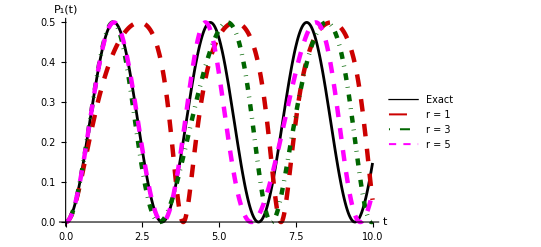

```mathematica
plot = Plot[{p1Exa,p1Trun1,p1Trun3,p1Trun5},{t,0,10},PlotStyle->{{Black,Thickness[0.005]},{RGBColor[0.8,0,0],Dashing[Medium],Thickness[0.008]},{RGBColor[0,0.4,0],DotDashed,Thickness[0.008]},{Magenta,Dashing[0.02],Thickness[0.008]}},AxesLabel->{"t","P_1(t)",FontSize->20},
PlotLegends->{"Exact","r = 1","r = 3","r = 5"}]
```

```mathematica
Export["JacobiAnger.pdf",plot]
```

JacobiAnger.pdf